(* Jose Dario Sanchez *)
(* josedario@ucla.edu *)
(* ID: 004-505-398 *)
(* HOMEWORK TWO (2) *)

```mathematica
(* 1) Solve the following for x(t):
x''[t], x'[0]==Vo, x[0]==Xo*)
```

```mathematica
solution1A=DSolveValue[{x''[t]==a,x[0]==Xo,x'[0]==Vo},x[t],t];
solution1A
```

1/2 (a t^2+2 t Vo+2 Xo)

```mathematica
(* 2) Solve the following for x1(t) and x2(t):
x''[t]+2*(k/m)*x[t]==(k/m)*y[t], y''[t]+2*(k/m)*x[t]==(k/m)*x[t], x[0]==0, x'[0]==0, y[0]==a,y'[0]==0}*)
```

```mathematica
diffEq2A=DSolve[{x''[t]+2*(k/m)*x[t]==(k/m)*y[t],y''[t]+2*(k/m)*x[t]==(k/m)*x[t],x[0]==0,x'[0]==0,y[0]==a,y'[0]==0},{x[t],y[t]},t][[1]];
solution2A=x[t]/.diffEq2A//FullSimplify
solution2B=y[t]/.diffEq2A//FullSimplify
```

(a √k t Sin[(√k t)/(√m)])/(2 √m)

a Cos[(√k t)/(√m)]+(a √k t Sin[(√k t)/(√m)])/(2 √m)

```mathematica
(* 3) Starting with equations (2.40),(2.41),(2,42) in Marion Example 2.7,reproduce the plot shown in Figure 2-8 (label this,and all other plots!)*)
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{(g+g Log[1-(k x Sec[theta])/Vo]+k Vo Sin[theta]-(1-(k x Sec[theta])/Vo) (g+k Vo Sin[theta]))/k^2}

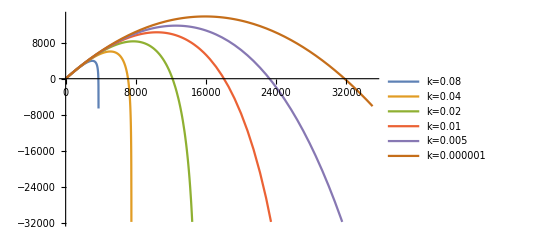

```mathematica
ClearAll["Global`*"]
diffEq3A=DSolve[{m*x''[t]+k*m*x'[t]==0,x'[0]==(Vo)*Cos[theta],x[0]==0},x[t],t];
diffEq3B=DSolve[{m*y''[t]+k*m*y'[t]+m*g==0,y'[0]==(Vo)*Sin[theta],y[0]==0},y[t],t];
solution2A=x[t]/.diffEq3A//FullSimplify;
solution2B=y[t]/.diffEq3B//FullSimplify;
solution2C=solution2A/.t->t[x];
t[x]=Normal[DSolveValue[x==solution2C,t[x],x]]//FullSimplify;
solution2D=solution2B/.t->t[x]

g=9.8;
Vo=600;
theta=Pi/3;

k1=0.08;
k2=0.04;
k3=0.02;
k4=0.01;
k5=0.005;
k6=0.000001;

plotFunction1=solution2D/.k->k1;
plotFunction2=solution2D/.k->k2;
plotFunction3=solution2D/.k->k3;
plotFunction4=solution2D/.k->k4;
plotFunction5=solution2D/.k->k5;
plotFunction6=solution2D/.k->k6;

Plot[{plotFunction1,plotFunction2,plotFunction3,plotFunction4,plotFunction5,plotFunction6},{x,0,35000},PlotLegends->{"k=0.08","k=0.04","k=0.02","k=0.01","k=0.005","k=0.000001"}]
```

```mathematica
(* 4)
–a) Define the following function:osc(t)=ẍ(t)+2βẋ(t)+ω2x(t)
–b) Solve the differential equation osc(t)=0 for x(t) subject to the
initial conditions ẋ(0)=0 and x(0)=1
–c)Plot x(t)fromt=0 to t=5 for the following cases: i)ω=2π,β=0 ii)ω=2π,β=4π,and iii)ω=2π,b=2π. Discuss the significance of each case.
```

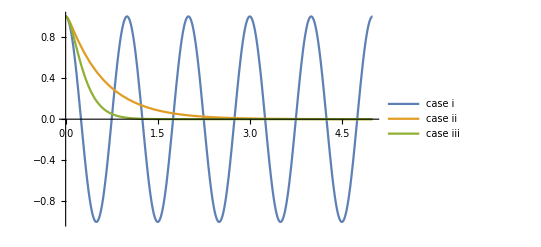

```mathematica
ClearAll["Global`*"]
osc[t]=x''[t]+2*B*x'[t]+(w^2)x[t];
x[t]=DSolveValue[{osc[t]==0,x'[0]==0,x[0]==1},x[t],t]//FullSimplify;

fun1=x[t]/.w->2*Pi/.B->0;
fun2=x[t]/.w->2*Pi/.B->4*Pi;
fun3=x[t]/.w->2*Pi/.B->(2*Pi+0.000001);

Plot[{Evaluate[fun1],fun2,fun3},{t,0,5},PlotLegends->{"case i","case ii","case iii"}]
```

```mathematica
(* Comments: First graph (in the blue) represents undamped motion. The amplitude of the oscillating cosine wave does not decrease as t approaches infinity. The second graph (in the yellow) represents overdamped motion in that it does dissipate over time, but much more slowly than the dissipation occuring in critically damped motion (seen in the green line). Overdamped motion has an opposing drag force slowing down the function from reaching the x axis. Critically damped has just enough opposition to keep it from overshooting and completing an oscillation to reach the x axis as quickly as possible.
```

```mathematica
(* 5) Marion 3-35. Not as bad as it looks. There are really only two temporal intervals,and Mathematica is going to do the hardest parts for you. Solve the first temporal interval as a driven oscillator,and use the relevant values at the end of that interval as initial conditions for the next interval. When you’re done, take β=π/2, ω=ω0=2π and a=1,and (on one plot) plot x(t) over the range 0<t<8π/ω0. Hint:Show[. . .].*)
```

```mathematica
Remove["Global`*"]
x1=DSolveValue[{x''[t]+2*B*x'[t]+(w)^2x[t]==(a)*Sin[w*t],x[0]==0,x'[0]==0},x[t],t]//FullSimplify;
D[x1,t]//FullSimplify;
x2=DSolveValue[{x''[t]+2*B*x'[t]+(w)^2x[t]==0},x[t],t]//FullSimplify;
x3=D[x2[t],t]//FullSimplify;

t=Pi/w;

Solve[x1==x2,C[1]]//FullSimplify;
DSolve[{x''[t]+2*B*x'[t]+(w)^2x[t]==0},x[t],t]//FullSimplify
```

```mathematica
(* Apologies! This block is lots of disorganized math I didn't know how to do any better when I made this! *)
Solve[(a (Sin[t w]-(ⅇ^(-B t) w Sinh[t √(B^2-w^2)])/(√((B-w) (B+w)))))/(2 B)==ⅇ^(-t (B+√((B-w) (B+w)))) (√((B-w) (B+w)) (-C[1]+ⅇ^(2 t √(B^2-w^2)) C[2])-B (C[1]+ⅇ^(2 t √(B^2-w^2)) C[2])),C[2]]//FullSimplify;
Solve[C[1]==1/(4 B w)(a (1+2 ⅇ^((π (B+√((B-w) (B+w))))/w)-B/(√((B-w) (B+w)))+ⅇ^((2 π √(B^2-w^2))/w) (1+B/(√((B-w) (B+w)))))-4 B ⅇ^((2 π √(B^2-w^2))/w) w (-(ⅇ^(-(2 π √(B^2-w^2))/w) (-a (-1+ⅇ^((2 π √(B^2-w^2))/w)) w+4 B (-w^2+B (B+√((B-w) (B+w)))) C[1]))/(4 B (w^2+B (-B+√((B-w) (B+w))))))),C[1]]//FullSimplify;
Solve[C[2]==-(ⅇ^(-(2 π √(B^2-w^2))/w) (-a (-1+ⅇ^((2 π √(B^2-w^2))/w)) w+4 B (-w^2+B (B+√((B-w) (B+w)))) ((a (1+ⅇ^((π (B+√((B-w) (B+w))))/w)) (-B+√((B-w) (B+w))))/(4 B w √((B-w) (B+w))))))/(4 B (w^2+B (-B+√((B-w) (B+w))))),C[2]]//FullSimplify;
w=Pi/t;
x[t]==ⅇ^(-t (B+√((B-w) (B+w)))) (((a (1+ⅇ^((π (B+√((B-w) (B+w))))/w)) (-B+√((B-w) (B+w))))/(4 B w √((B-w) (B+w))))+ⅇ^(2 t √(B^2-w^2)) (-(a (1+ⅇ^((π (B-√((B-w) (B+w))))/w)) w)/(4 B (B^2-w^2-B √((B-w) (B+w))))))//FullSimplify;
(a ⅇ^(-(t (B+√((B-w) (B+w))))/1) (1+2 ⅇ^((t (B+√((B-w) (B+w))))/1)-B/(√((B-w) (B+w)))+ⅇ^((2 t √(B^2-w^2))/1) (1+B/(√((B-w) (B+w))))))/(4 B w)//FullSimplify;
(a ⅇ^(-(B+√((B-π/t) (B+π/t))) t) (1+2 ⅇ^((B+√((B-π/t) (B+π/t))) t)+ⅇ^(2 √(B^2-π^2/t^2) t) (1+B/(√((B-π/t) (B+π/t))))-B/(√((B-π/t) (B+π/t)))) t)/(4 B π)//FullSimplify;
-(a (Cos[t w]+ⅇ^(-B t) (-Cosh[t √(B^2-w^2)]-(B Sinh[t √(B^2-w^2)])/(√((B-w) (B+w))))))/(2 B w)//FullSimplify;
```

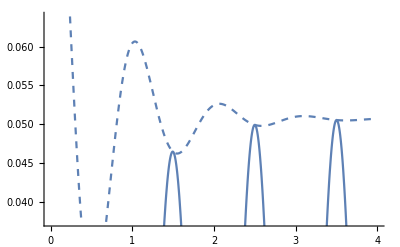

```mathematica
ClearAll["Global`*"]

B=Pi/2;
w=2*Pi;
a=1;
Show[Plot[(30+2 ⅇ^(-(π t)/2) (15 Cos[1/2 √15 π t]+√15 Sin[1/2 √15 π t]))/(60 π^2),{t,0,(8*Pi/w)},PlotLegends->"First Interval (Dashed)",PlotStyle->Dashed],Plot[-(a (Cos[t w]+ⅇ^(-B t) (-Cosh[t √(B^2-w^2)]-(B Sinh[t √(B^2-w^2)])/(√((B-w) (B+w))))))/(2 B w),{t,0,8*Pi/w},PlotLegends->"Second Interval (Solid)"]]
```